```mathematica
"definição do raio do Sinai"
a=5
```

```mathematica
"definição do retângulo"
A=21
B=14
```

definição do retângulo

21

14

```mathematica
"definição da barreira de potencial Ka"
Ka=1000
```

definição da barreira de potencial Ka

1000

```mathematica
"definição da base harmonica e de seus autovalores"
φ[x_,y_,n_,m_]=2/(√(A*B))Sin[π*n(x/A)]Sin[π*m(y/B)]
nM=10
mM=10
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
κ[n_,m_]=π √((n/A)^2+(m/B)^2)
```

definição da base harmonica e de seus autovalores

1/7 √(2/3) Sin[(n π x)/21] Sin[(m π y)/14]

10

10

{1/7 √(2/3) Sin[(π x)/21] Sin[(π y)/14],1/7 √(2/3) Sin[(2 π x)/21] Sin[(π y)/14],1/7 √(2/3) Sin[(π x)/7] Sin[(π y)/14],1/7 √(2/3) Sin[(4 π x)/21] Sin[(π y)/14],1/7 √(2/3) Sin[(5 π x)/21] Sin[(π y)/14],1/7 √(2/3) Sin[(2 π x)/7] Sin[(π y)/14],1/7 √(2/3) Sin[(π x)/3] Sin[(π y)/14],1/7 √(2/3) Sin[(8 π x)/21] Sin[(π y)/14],1/7 √(2/3) Sin[(3 π x)/7] Sin[(π y)/14],1/7 √(2/3) Sin[(10 π x)/21] Sin[(π y)/14],1/7 √(2/3) Sin[(π x)/21] Sin[(π y)/7],1/7 √(2/3) Sin[(2 π x)/21] Sin[(π y)/7],1/7 √(2/3) Sin[(π x)/7] Sin[(π y)/7],1/7 √(2/3) Sin[(4 π x)/21] Sin[(π y)/7],1/7 √(2/3) Sin[(5 π x)/21] Sin[(π y)/7],1/7 √(2/3) Sin[(2 π x)/7] Sin[(π y)/7],1/7 √(2/3) Sin[(π x)/3] Sin[(π y)/7],1/7 √(2/3) Sin[(8 π x)/21] Sin[(π y)/7],1/7 √(2/3) Sin[(3 π x)/7] Sin[(π y)/7],1/7 √(2/3) Sin[(10 π x)/21] Sin[(π y)/7],1/7 √(2/3) Sin[(π x)/21] Sin[(3 π y)/14],1/7 √(2/3) Sin[(2 π x)/21] Sin[(3 π y)/14],1/7 √(2/3) Sin[(π x)/7] Sin[(3 π y)/14],1/7 √(2/3) Sin[(4 π x)/21] Sin[(3 π y)/14],1/7 √(2/3) Sin[(5 π x)/21] Sin[(3 π y)/14],1/7 √(2/3) Sin[(2 π x)/7] Sin[(3 π y)/14],1/7 √(2/3) Sin[(π x)/3] Sin[(3 π y)/14],1/7 √(2/3) Sin[(8 π x)/21] Sin[(3 π y)/14],1/7 √(2/3) Sin[(3 π x)/7] Sin[(3 π y)/14],1/7 √(2/3) Sin[(10 π x)/21] Sin[(3 π y)/14],1/7 √(2/3) Sin[(π x)/21] Sin[(2 π y)/7],1/7 √(2/3) Sin[(2 π x)/21] Sin[(2 π y)/7],1/7 √(2/3) Sin[(π x)/7] Sin[(2 π y)/7],1/7 √(2/3) Sin[(4 π x)/21] Sin[(2 π y)/7],1/7 √(2/3) Sin[(5 π x)/21] Sin[(2 π y)/7],1/7 √(2/3) Sin[(2 π x)/7] Sin[(2 π y)/7],1/7 √(2/3) Sin[(π x)/3] Sin[(2 π y)/7],1/7 √(2/3) Sin[(8 π x)/21] Sin[(2 π y)/7],1/7 √(2/3) Sin[(3 π x)/7] Sin[(2 π y)/7],1/7 √(2/3) Sin[(10 π x)/21] Sin[(2 π y)/7],1/7 √(2/3) Sin[(π x)/21] Sin[(5 π y)/14],1/7 √(2/3) Sin[(2 π x)/21] Sin[(5 π y)/14],1/7 √(2/3) Sin[(π x)/7] Sin[(5 π y)/14],1/7 √(2/3) Sin[(4 π x)/21] Sin[(5 π y)/14],1/7 √(2/3) Sin[(5 π x)/21] Sin[(5 π y)/14],1/7 √(2/3) Sin[(2 π x)/7] Sin[(5 π y)/14],1/7 √(2/3) Sin[(π x)/3] Sin[(5 π y)/14],1/7 √(2/3) Sin[(8 π x)/21] Sin[(5 π y)/14],1/7 √(2/3) Sin[(3 π x)/7] Sin[(5 π y)/14],1/7 √(2/3) Sin[(10 π x)/21] Sin[(5 π y)/14],1/7 √(2/3) Sin[(π x)/21] Sin[(3 π y)/7],1/7 √(2/3) Sin[(2 π x)/21] Sin[(3 π y)/7],1/7 √(2/3) Sin[(π x)/7] Sin[(3 π y)/7],1/7 √(2/3) Sin[(4 π x)/21] Sin[(3 π y)/7],1/7 √(2/3) Sin[(5 π x)/21] Sin[(3 π y)/7],1/7 √(2/3) Sin[(2 π x)/7] Sin[(3 π y)/7],1/7 √(2/3) Sin[(π x)/3] Sin[(3 π y)/7],1/7 √(2/3) Sin[(8 π x)/21] Sin[(3 π y)/7],1/7 √(2/3) Sin[(3 π x)/7] Sin[(3 π y)/7],1/7 √(2/3) Sin[(10 π x)/21] Sin[(3 π y)/7],1/7 √(2/3) Sin[(π x)/21] Sin[(π y)/2],1/7 √(2/3) Sin[(2 π x)/21] Sin[(π y)/2],1/7 √(2/3) Sin[(π x)/7] Sin[(π y)/2],1/7 √(2/3) Sin[(4 π x)/21] Sin[(π y)/2],1/7 √(2/3) Sin[(5 π x)/21] Sin[(π y)/2],1/7 √(2/3) Sin[(2 π x)/7] Sin[(π y)/2],1/7 √(2/3) Sin[(π x)/3] Sin[(π y)/2],1/7 √(2/3) Sin[(8 π x)/21] Sin[(π y)/2],1/7 √(2/3) Sin[(3 π x)/7] Sin[(π y)/2],1/7 √(2/3) Sin[(10 π x)/21] Sin[(π y)/2],1/7 √(2/3) Sin[(π x)/21] Sin[(4 π y)/7],1/7 √(2/3) Sin[(2 π x)/21] Sin[(4 π y)/7],1/7 √(2/3) Sin[(π x)/7] Sin[(4 π y)/7],1/7 √(2/3) Sin[(4 π x)/21] Sin[(4 π y)/7],1/7 √(2/3) Sin[(5 π x)/21] Sin[(4 π y)/7],1/7 √(2/3) Sin[(2 π x)/7] Sin[(4 π y)/7],1/7 √(2/3) Sin[(π x)/3] Sin[(4 π y)/7],1/7 √(2/3) Sin[(8 π x)/21] Sin[(4 π y)/7],1/7 √(2/3) Sin[(3 π x)/7] Sin[(4 π y)/7],1/7 √(2/3) Sin[(10 π x)/21] Sin[(4 π y)/7],1/7 √(2/3) Sin[(π x)/21] Sin[(9 π y)/14],1/7 √(2/3) Sin[(2 π x)/21] Sin[(9 π y)/14],1/7 √(2/3) Sin[(π x)/7] Sin[(9 π y)/14],1/7 √(2/3) Sin[(4 π x)/21] Sin[(9 π y)/14],1/7 √(2/3) Sin[(5 π x)/21] Sin[(9 π y)/14],1/7 √(2/3) Sin[(2 π x)/7] Sin[(9 π y)/14],1/7 √(2/3) Sin[(π x)/3] Sin[(9 π y)/14],1/7 √(2/3) Sin[(8 π x)/21] Sin[(9 π y)/14],1/7 √(2/3) Sin[(3 π x)/7] Sin[(9 π y)/14],1/7 √(2/3) Sin[(10 π x)/21] Sin[(9 π y)/14],1/7 √(2/3) Sin[(π x)/21] Sin[(5 π y)/7],1/7 √(2/3) Sin[(2 π x)/21] Sin[(5 π y)/7],1/7 √(2/3) Sin[(π x)/7] Sin[(5 π y)/7],1/7 √(2/3) Sin[(4 π x)/21] Sin[(5 π y)/7],1/7 √(2/3) Sin[(5 π x)/21] Sin[(5 π y)/7],1/7 √(2/3) Sin[(2 π x)/7] Sin[(5 π y)/7],1/7 √(2/3) Sin[(π x)/3] Sin[(5 π y)/7],1/7 √(2/3) Sin[(8 π x)/21] Sin[(5 π y)/7],1/7 √(2/3) Sin[(3 π x)/7] Sin[(5 π y)/7],1/7 √(2/3) Sin[(10 π x)/21] Sin[(5 π y)/7]}

√(m^2/196+n^2/441) π

```mathematica
"definição da matriz M que depende da barreira de potencial Ka"
M = Table[κ[1+Mod[j,nM],1+(j-Mod[j,nM])/mM]^2 KroneckerDelta[i,j]+ Ka^2NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,B-a,B},{x,A-√(a^2-(y-B)^2),A},AccuracyGoal->30],{i,0,nM*mM-1},{j,0,nM*mM-1}] 
M // MatrixForm
```

definição da matriz M que depende da barreira de potencial Ka

{{6238.77,-11188.5,13912.,-14063.2,11944.5,-8369.82,4389.42,-972.304,-1249.51,2100.86,-9790.26,17455.,-21467.2,21303.,«72»,3250.43,-3211.71,2620.84,-1507.05,-515.849,1022.63,-1494.08,1875.9,-2086.89,2035.63,-1651.54,922.64,73.9219,-1164.64},«99»}

(«1»)

```mathematica
"lista de autovalores e autofunções(para uma barreira Ka) da matriz M"
Lista = N[Eigensystem[M]]
```

lista de autovalores e autofunções(para uma barreira Ka) da matriz M

{{999672.,996055.,932413.,916934.,809861.,438148.,320832.,227841.,113049.,60267.4,22492.1,8286.2,2861.41,2383.39,«72»,0.864346,0.840997,0.807682,0.697491,0.641419,0.590889,0.530598,0.487638,0.420429,0.365942,0.274542,0.23899,0.165084,0.0823401},{«1»}}

```mathematica
"autofunção normalizada(para um dado autovalor k de indice id e barreira Ka) da matriz M"
id=nM*mM-8
ConsNorm =Lista[[2]][[id]].Lista[[2]][[id]]
ListaAutovalores2=Table[κ[1+Mod[i,nM],1+(i-Mod[i,nM])/mM]^2,{i,0,nM*mM-1}]
ListaCons2 = Table[(Lista[[2]][[id]][[1+i]])^2,{i,0,nM*mM-1}]
k=ListaAutovalores2.ListaCons2/ConsNorm 
ϕ[x_,y_]=Base[x,y].Lista[[2]][[id]]/ConsNorm
```

autofunção normalizada(para um dado autovalor k de indice id e barreira Ka) da matriz M

92

1.

{(13 π^2)/1764,(25 π^2)/1764,(5 π^2)/196,(73 π^2)/1764,(109 π^2)/1764,(17 π^2)/196,(205 π^2)/1764,(265 π^2)/1764,(37 π^2)/196,(409 π^2)/1764,(10 π^2)/441,(13 π^2)/441,(2 π^2)/49,(25 π^2)/441,(34 π^2)/441,(5 π^2)/49,(58 π^2)/441,(73 π^2)/441,(10 π^2)/49,(109 π^2)/441,(85 π^2)/1764,(97 π^2)/1764,(13 π^2)/196,(145 π^2)/1764,(181 π^2)/1764,(25 π^2)/196,(277 π^2)/1764,(337 π^2)/1764,(45 π^2)/196,(481 π^2)/1764,(37 π^2)/441,(40 π^2)/441,(5 π^2)/49,(52 π^2)/441,(61 π^2)/441,(8 π^2)/49,(85 π^2)/441,(100 π^2)/441,(13 π^2)/49,(136 π^2)/441,(229 π^2)/1764,(241 π^2)/1764,(29 π^2)/196,(289 π^2)/1764,(325 π^2)/1764,(41 π^2)/196,(421 π^2)/1764,(481 π^2)/1764,(61 π^2)/196,(625 π^2)/1764,(82 π^2)/441,(85 π^2)/441,(10 π^2)/49,(97 π^2)/441,(106 π^2)/441,(13 π^2)/49,(130 π^2)/441,(145 π^2)/441,(18 π^2)/49,(181 π^2)/441,(445 π^2)/1764,(457 π^2)/1764,(53 π^2)/196,(505 π^2)/1764,(541 π^2)/1764,(65 π^2)/196,(13 π^2)/36,(697 π^2)/1764,(85 π^2)/196,(841 π^2)/1764,(145 π^2)/441,(148 π^2)/441,(17 π^2)/49,(160 π^2)/441,(169 π^2)/441,(20 π^2)/49,(193 π^2)/441,(208 π^2)/441,(25 π^2)/49,(244 π^2)/441,(733 π^2)/1764,(745 π^2)/1764,(85 π^2)/196,(793 π^2)/1764,(829 π^2)/1764,(97 π^2)/196,(925 π^2)/1764,(985 π^2)/1764,(117 π^2)/196,(1129 π^2)/1764,(226 π^2)/441,(229 π^2)/441,(26 π^2)/49,(241 π^2)/441,(250 π^2)/441,(29 π^2)/49,(274 π^2)/441,(289 π^2)/441,(34 π^2)/49,(325 π^2)/441}

{0.0000164326,4.98168×10^-6,0.000734565,0.00676699,0.339786,0.000141817,0.0010418,0.000436651,1.79459×10^-6,0.0000211521,0.000577269,0.000484621,0.00150114,0.389692,0.0104418,7.561×10^-6,0.000981451,0.000432184,9.6175×10^-6,0.0000237344,0.025296,0.184246,0.00682924,0.00439414,0.00198717,0.000033761,0.000216229,0.0000614526,0.0000906443,4.24308×10^-7,0.00991351,0.00942302,0.00125542,0.000128735,0.000382461,0.0000304027,0.0000257613,1.41376×10^-7,0.000119933,0.0000156777,0.000701179,0.000861757,0.000128856,0.0000417972,0.0000852925,9.4275×10^-7,0.0000243841,3.33282×10^-8,0.000056253,0.0000231973,0.0000184358,5.08199×10^-6,0.0000215639,0.0000779814,0.0000288685,6.77562×10^-6,0.0000491293,9.66082×10^-6,0.0000135856,4.55119×10^-6,4.58177×10^-6,0.0000262625,0.0000585431,0.000049142,5.57232×10^-6,0.0000122596,0.0000346555,7.18894×10^-6,5.88187×10^-6,1.30218×10^-7,4.16428×10^-7,1.94156×10^-6,2.90185×10^-6,8.10934×10^-7,9.06019×10^-7,5.93879×10^-6,3.62373×10^-6,5.28635×10^-7,7.77787×10^-6,1.00271×10^-8,2.60291×10^-6,7.42618×10^-6,9.79066×10^-6,8.45525×10^-6,4.27729×10^-6,3.15222×10^-7,2.09911×10^-6,9.14608×10^-6,5.88485×10^-6,3.54782×10^-6,1.59799×10^-7,6.10444×10^-7,1.05503×10^-6,9.88894×10^-7,4.48187×10^-7,5.16536×10^-8,1.28826×10^-8,1.06175×10^-7,3.1862×10^-7,6.1401×10^-7}

0.587286

1. (0.000472835 Sin[(π x)/21] Sin[(π y)/14]+0.000260342 Sin[(2 π x)/21] Sin[(π y)/14]-0.00316134 Sin[(π x)/7] Sin[(π y)/14]+0.0095952 Sin[(4 π x)/21] Sin[(π y)/14]+0.0679922 Sin[(5 π x)/21] Sin[(π y)/14]+0.00138906 Sin[(2 π x)/7] Sin[(π y)/14]-0.00376486 Sin[(π x)/3] Sin[(π y)/14]+0.00243738 Sin[(8 π x)/21] Sin[(π y)/14]-0.000156257 Sin[(3 π x)/7] Sin[(π y)/14]-0.000536454 Sin[(10 π x)/21] Sin[(π y)/14]-0.0028025 Sin[(π x)/21] Sin[(π y)/7]+0.00256778 Sin[(2 π x)/21] Sin[(π y)/7]+0.00451925 Sin[(π x)/7] Sin[(π y)/7]-0.0728144 Sin[(4 π x)/21] Sin[(π y)/7]-0.0119191 Sin[(5 π x)/21] Sin[(π y)/7]-0.000320735 Sin[(2 π x)/7] Sin[(π y)/7]+0.00365419 Sin[(π x)/3] Sin[(π y)/7]-0.00242488 Sin[(8 π x)/21] Sin[(π y)/7]-0.000361732 Sin[(3 π x)/7] Sin[(π y)/7]+0.000568257 Sin[(10 π x)/21] Sin[(π y)/7]+0.0185516 Sin[(π x)/21] Sin[(3 π y)/14]-0.0500674 Sin[(2 π x)/21] Sin[(3 π y)/14]-0.00963924 Sin[(π x)/7] Sin[(3 π y)/14]-0.00773203 Sin[(4 π x)/21] Sin[(3 π y)/14]+0.00519965 Sin[(5 π x)/21] Sin[(3 π y)/14]-0.000677741 Sin[(2 π x)/7] Sin[(3 π y)/14]-0.0017152 Sin[(π x)/3] Sin[(3 π y)/14]+0.000914379 Sin[(8 π x)/21] Sin[(3 π y)/14]+0.00111052 Sin[(3 π x)/7] Sin[(3 π y)/14]-0.0000759796 Sin[(10 π x)/21] Sin[(3 π y)/14]+0.0116137 Sin[(π x)/21] Sin[(2 π y)/7]-0.0113227 Sin[(2 π x)/21] Sin[(2 π y)/7]+0.00413287 Sin[(π x)/7] Sin[(2 π y)/7]+0.00132344 Sin[(4 π x)/21] Sin[(2 π y)/7]-0.00228113 Sin[(5 π x)/21] Sin[(2 π y)/7]+0.00064315 Sin[(2 π x)/7] Sin[(2 π y)/7]+0.000592025 Sin[(π x)/3] Sin[(2 π y)/7]+0.0000438575 Sin[(8 π x)/21] Sin[(2 π y)/7]-0.0012774 Sin[(3 π x)/7] Sin[(2 π y)/7]-0.000461846 Sin[(10 π x)/21] Sin[(2 π y)/7]-0.00308867 Sin[(π x)/21] Sin[(5 π y)/14]+0.00342412 Sin[(2 π x)/21] Sin[(5 π y)/14]-0.00132406 Sin[(π x)/7] Sin[(5 π y)/14]-0.000754102 Sin[(4 π x)/21] Sin[(5 π y)/14]+0.00107724 Sin[(5 π x)/21] Sin[(5 π y)/14]-0.000113254 Sin[(2 π x)/7] Sin[(5 π y)/14]-0.000575983 Sin[(π x)/3] Sin[(5 π y)/14]+0.0000212942 Sin[(8 π x)/21] Sin[(5 π y)/14]+0.000874841 Sin[(3 π x)/7] Sin[(5 π y)/14]+0.000561791 Sin[(10 π x)/21] Sin[(5 π y)/14]+0.000500827 Sin[(π x)/21] Sin[(3 π y)/7]-0.00026295 Sin[(2 π x)/21] Sin[(3 π y)/7]-0.000541651 Sin[(π x)/7] Sin[(3 π y)/7]+0.00103003 Sin[(4 π x)/21] Sin[(3 π y)/7]-0.000626713 Sin[(5 π x)/21] Sin[(3 π y)/7]-0.00030362 Sin[(2 π x)/7] Sin[(3 π y)/7]+0.000817573 Sin[(π x)/3] Sin[(3 π y)/7]-0.000362546 Sin[(8 π x)/21] Sin[(3 π y)/7]-0.000429929 Sin[(3 π x)/7] Sin[(3 π y)/7]-0.000248839 Sin[(10 π x)/21] Sin[(3 π y)/7]+0.000249674 Sin[(π x)/21] Sin[(π y)/2]-0.000597757 Sin[(2 π x)/21] Sin[(π y)/2]+0.000892471 Sin[(π x)/7] Sin[(π y)/2]-0.000817679 Sin[(4 π x)/21] Sin[(π y)/2]+0.000275343 Sin[(5 π x)/21] Sin[(π y)/2]+0.000408409 Sin[(2 π x)/7] Sin[(π y)/2]-0.000686661 Sin[(π x)/3] Sin[(π y)/2]+0.000312744 Sin[(8 π x)/21] Sin[(π y)/2]+0.000282888 Sin[(3 π x)/7] Sin[(π y)/2]-0.0000420913 Sin[(10 π x)/21] Sin[(π y)/2]-0.0000752708 Sin[(π x)/21] Sin[(4 π y)/7]+0.000162529 Sin[(2 π x)/21] Sin[(4 π y)/7]-0.000198698 Sin[(π x)/7] Sin[(4 π y)/7]+0.000105039 Sin[(4 π x)/21] Sin[(4 π y)/7]+0.000111026 Sin[(5 π x)/21] Sin[(4 π y)/7]-0.000284253 Sin[(2 π x)/7] Sin[(4 π y)/7]+0.000222042 Sin[(π x)/3] Sin[(4 π y)/7]+0.0000848075 Sin[(8 π x)/21] Sin[(4 π y)/7]-0.000325302 Sin[(3 π x)/7] Sin[(4 π y)/7]-0.00001168 Sin[(10 π x)/21] Sin[(4 π y)/7]-0.000188185 Sin[(π x)/21] Sin[(9 π y)/14]+0.000317862 Sin[(2 π x)/21] Sin[(9 π y)/14]-0.000364974 Sin[(π x)/7] Sin[(9 π y)/14]+0.000339172 Sin[(4 π x)/21] Sin[(9 π y)/14]-0.000241235 Sin[(5 π x)/21] Sin[(9 π y)/14]+0.0000654885 Sin[(2 π x)/7] Sin[(9 π y)/14]+0.000168995 Sin[(π x)/3] Sin[(9 π y)/14]-0.000352755 Sin[(8 π x)/21] Sin[(9 π y)/14]+0.000282959 Sin[(3 π x)/7] Sin[(9 π y)/14]+0.000219704 Sin[(10 π x)/21] Sin[(9 π y)/14]-0.0000466276 Sin[(π x)/21] Sin[(5 π y)/7]+0.0000911338 Sin[(2 π x)/21] Sin[(5 π y)/7]-0.000119809 Sin[(π x)/7] Sin[(5 π y)/7]+0.000115993 Sin[(4 π x)/21] Sin[(5 π y)/7]-0.0000780883 Sin[(5 π x)/21] Sin[(5 π y)/7]+0.0000265098 Sin[(2 π x)/7] Sin[(5 π y)/7]+0.0000132391 Sin[(π x)/3] Sin[(5 π y)/7]-0.0000380073 Sin[(8 π x)/21] Sin[(5 π y)/7]+0.0000658404 Sin[(3 π x)/7] Sin[(5 π y)/7]-0.0000913996 Sin[(10 π x)/21] Sin[(5 π y)/7])

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(x-A)^2+(y-B)^2≥ a^2]]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

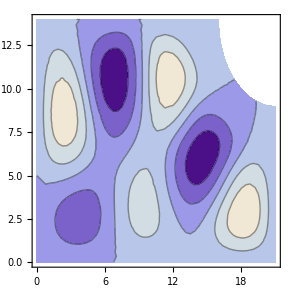

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(x-A)^2+(y-B)^2≥ a^2]]
```

curvas nodais da autofunção

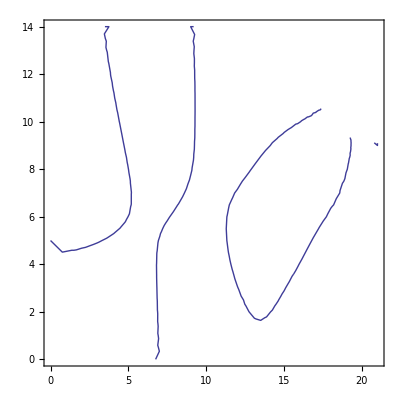

```mathematica
"curvas nodais da autofunção"
ContourPlot[ϕ[x,y]==0,{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(x-A)^2+(y-B)^2≥ a^2]]
```